1500.91

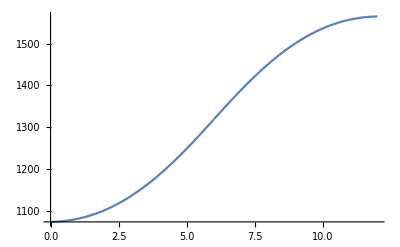

```mathematica
(*Kodutöö NR 2
Siim Erik Pugal
179411YAFB*)
MinuPytt[R_,L_,l_,H_]:=Module[{Vs,Vk},
If[H<0,"Mahutis pole vett",If[H>2*R,"Vedeliku kõrgus ületab mahuti diameetri",Vs=π*R^2*L/2+R^2*ArcSin[(H-R)/R]+(H-R)*Sqrt[2*H*R-H^2];If[H≤ R,d=R-H;Vk=NIntegrate[l/R*(r^2*ArcCos[d/r]-d*Sqrt[r^2-d^2]),{r,d,R}];N[Vs+2*Vk],d=H-R;Vk=NIntegrate[l/R*(r^2*ArcCos[d/r]-d*Sqrt[r^2-d^2]),{r,d,R}];N[Vs+2*(π*R^2*l/3-Vk)]
]]]
]

MinuPytt[6,20,5,9]
Plot[MinuPytt[6,20,5,h],{h,0,12}]
```